Your Title Here

```mathematica
H1T=Quiet@Interpolation@{(*{T (K), H (kJ/kg)},*){273.,21.02},{278.,42.02},{283.,62.98},{288.,83.91},{293.,104.83},{298.,125.73},{303.,146.63},{308.,167.53},{313.,188.43},{318.,209.34},{323.,230.26},{328.,251.18},{333.,272.12},{338.,293.07},{343.,314.03},{348.,335.01},{353.,356.01},{358.,377.04},{363.,398.09},{368.,419.17},{373.,461.42},{383.,503.81},{393.,546.38},{403.,589.16},{413.,632.18},{423.,675.47},{433.,719.08},{443.,763.05},{453.,807.43},{463.,852.27},{473.,897.63},{483.,943.58},{493.,990.19},{503.,1037.6},{513.,1085.8},{523.,1135.},{533.,1185.3},{543.,1236.9},{553.,1290.},{563.,1345.},{573.,1402.2},{583.,1462.2},{593.,1525.9},{603.,1594.5},{613.,1670.9},{623.,1761.7},{633.,1890.7},{643.,2084.3}};
```

```mathematica
HLP=Quiet@Interpolation@{(*{P (MPa), HL (kJ/kg)},*){0.0006,0.001},{0.0009,21.02},{0.0012,42.021},{0.0017,62.981},{0.0023,83.914},{0.0032,104.83},{0.0042,125.73},{0.0056,146.63},{0.0074,167.53},{0.0096,188.43},{0.0124,209.34},{0.0158,230.26},{0.0199,251.18},{0.025,272.12},{0.031200,293.07},{0.0386,314.03},{0.0474,335.01},{0.0579,356.01},{0.0702,377.04},{0.0846,398.09},{0.1014,419.17},{0.1434,461.42},{0.19870,503.81},{0.2703,546.38},{0.3615,589.16},{0.4762,632.18},{0.61820,675.47},{0.7922,719.08},{1.00280,763.05},{1.2552,807.43},{1.5549,852.27},{1.9077,897.63},{2.3196,943.58},{2.7971,990.19},{3.3469,1037.60},{3.9762,1085.8},{4.6923,1135.},{5.503,1185.3},{6.4166,1236.9},{7.4418,1290.},{8.5879,1345.},{9.8651,1402.2},{11.284,1462.2},{12.858,1525.9},{14.601,1594.5},{16.529,1670.9},{18.666,1761.7},{21.044,1890.7},{22.064,2084.3}};
```

```mathematica
HVP=Quiet@Interpolation@{(*{P (MPa), HV (kJ/kg)},*){0.00061,2500.9},{0.00087,2510.1},{0.0012300,2519.2},{0.00171,2528.3},{0.00234,2537.4},{0.00317,2546.5},{0.00425,2555.5},{0.00563,2564.5},{0.00738,2573.5},{0.00959,2582.4},{0.012350,2591.3},{0.01576,2600.1},{0.019950,2608.8},{0.025040,2617.5},{0.031200,2626.1},{0.03859,2634.6},{0.04741,2643.},{0.05787,2651.3},{0.07018,2659.5},{0.08461,2667.6},{0.101420,2675.6},{0.14338,2691.1},{0.19867,2705.9},{0.27028,2720.1},{0.36154,2733.4},{0.47616,2745.9},{0.61823,2757.4},{0.79219,2767.9},{1.00280,2777.2},{1.2552,2785.3},{1.5549,2792.},{1.9077,2797.3},{2.3196,2800.9},{2.7971,2802.9},{3.3469,2803.},{3.9762,2800.9},{4.6923,2796.6},{5.503,2789.7},{6.4166,2779.9},{7.4418,2766.7},{8.5879,2749.6},{9.8651,2727.9},{11.284,2700.6},{12.858,2666.},{14.601,2621.8},{16.529,2563.6},{18.666,2481.5},{21.044,2334.5},{22.064,2084.3}};
```

```mathematica
TP=Quiet@Interpolation@{(*{P (MPa), T (K)}*){0.0006,273.01},{0.0009,278.},{0.0012,283.},{0.0017,288.},{0.0023,293.},{0.0032,298.},{0.0042,303.},{0.0056,308.},{0.0074,313.},{0.0096,318.},{0.0124,323.},{0.0158,328.},{0.0199,333.},{0.025,338.},{0.0312,343.},{0.0386,348.},{0.0474,353.},{0.0579,358.},{0.0702,363.},{0.0846,368.},{0.1014,373.},{0.1434,383.},{0.1987,393.},{0.2703,403.},{0.3615,413.},{0.4762,423.},{0.6182,433.},{0.7922,443.},{1.0028,453.},{1.2552,463.},{1.5549,473.},{1.9077,483.},{2.3196,493.},{2.7971,503.},{3.3469,513.},{3.9762,523.},{4.6923,533.},{5.503,543.},{6.4166,553.},{7.4418,563.},{8.5879,573.},{9.8651,583.},{11.284,593.},{12.858,603.},{14.601,613.},{16.529,623.},{18.666,633.},{21.044,643.},{22.064,646.95}};
```

```mathematica
(*COMPRESSED LIQUID*)
```

```mathematica
P01=Quiet@Interpolation[{{0.1,273.16},{21.161,278.16},{42.16,283.16},{63.117,288.16},{84.048,293.16},{104.96,298.16},{125.86,303.16},{146.76,308.16},{167.66,313.16},{188.56,318.16},{209.46,323.16},{230.37,328.16},{251.29,333.16},{272.22,338.16},{293.16,343.16},{314.12,348.16},{335.1,353.16},{356.09,358.16},{377.1,363.16},{398.14,368.16},{417.5,372.76},{2674.9,372.76},{2675.8,373.16},{2686.1,378.16},{2696.4,383.16},{2706.5,388.16},{2716.7,393.16},{2726.7,398.16},{2736.8,403.16},{2746.8,408.16},{2756.7,413.16},{2766.7,418.16},{2776.6,423.16},{2786.5,428.16},{2796.4,433.16},{2806.3,438.16},{2816.2,443.16},{2826.1,448.16},{2836.,453.16},{2845.8,458.16},{2855.7,463.16},{2865.6,468.16},{2875.5,473.16},{2885.3,478.16},{2895.2,483.16},{2905.1,488.16},{2915.,493.16},{2924.9,498.16},{2934.8,503.16},{2944.7,508.16},{2954.7,513.16},{2964.6,518.16},{2974.5,523.16},{2984.5,528.16},{2994.4,533.16},{3004.4,538.16},{3014.4,543.16},{3024.4,548.16},{3034.4,553.16},{3044.4,558.16},{3054.5,563.16},{3064.5,568.16},{3074.6,573.16},{3084.6,578.16},{3094.7,583.16},{3104.8,588.16},{3114.9,593.16},{3125.,598.16},{3135.2,603.16},{3145.3,608.16},{3155.5,613.16},{3165.7,618.16},{3175.8,623.16},{3186.1,628.16},{3196.3,633.16},{3206.5,638.16},{3216.8,643.16},{3227.,648.16}},InterpolationOrder->1];
```

```mathematica
P02=Quiet@Interpolation[{{0.1,273.1},{0.2,273.16},{21.26,278.16},{42.26,283.16},{63.21,288.16},{84.14,293.16},{105.05,298.16},{125.95,303.16},{146.85,308.16},{167.75,313.16},{188.64,318.16},{209.55,323.16},{230.45,328.16},{251.37,333.16},{272.3,338.16},{293.25,343.16},{314.2,348.16},{335.18,353.16},{356.17,358.16},{377.18,363.16},{398.22,368.16},{419.28,373.16},{440.37,378.16},{461.5,383.16},{482.66,388.16},{503.86,393.16},{504.7,393.36},{2706.2,393.36},{2716.6,398.16},{2727.3,403.16},{2737.9,408.16},{2748.3,413.16},{2758.8,418.16},{2769.1,423.16},{2779.4,428.16},{2789.7,433.16},{2799.9,438.16},{2810.1,443.16},{2820.2,448.16},{2830.4,453.16},{2840.5,458.16},{2850.6,463.16},{2860.7,468.16},{2870.8,473.16},{2880.8,478.16},{2890.9,483.16},{2900.9,488.16},{2911.,493.16},{2921.,498.16},{2931.,503.16},{2941.1,508.16},{2951.1,513.16},{2961.2,518.16},{2971.2,523.16},{2981.3,528.16},{2991.3,533.16},{3001.4,538.16},{3011.5,543.16},{3021.6,548.16},{3031.7,553.16},{3041.7,558.16},{3051.9,563.16},{3062.,568.16},{3072.1,573.16},{3082.2,578.16},{3092.4,583.16},{3102.5,588.16},{3112.7,593.16},{3122.9,598.16},{3133.,603.16},{3143.2,608.16},{3153.5,613.16},{3163.7,618.16},{3173.9,623.16},{3184.2,628.16},{3194.4,633.16},{3204.7,638.16},{3215.,643.16},{3225.3,648.16}},InterpolationOrder->1];
```

```mathematica
P03=Quiet@Interpolation[{{0.1,273.1},{0.31,273.16},{21.36,278.16},{42.36,283.16},{63.31,288.16},{84.24,293.16},{105.15,298.16},{126.05,303.16},{146.94,308.16},{167.83,313.16},{188.73,318.16},{209.63,323.16},{230.54,328.16},{251.46,333.16},{272.39,338.16},{293.33,343.16},{314.28,348.16},{335.26,353.16},{356.25,358.16},{377.26,363.16},{398.3,368.16},{419.36,373.16},{440.45,378.16},{461.57,383.16},{482.73,388.16},{503.93,393.16},{525.16,398.16},{546.45,403.16},{561.43,406.67},{2724.9,406.67},{2728.2,408.16},{2739.4,413.16},{2750.4,418.16},{2761.2,423.16},{2772.,428.16},{2782.6,433.16},{2793.2,438.16},{2803.7,443.16},{2814.2,448.16},{2824.6,453.16},{2835.,458.16},{2845.3,463.16},{2855.6,468.16},{2865.9,473.16},{2876.2,478.16},{2886.4,483.16},{2896.6,488.16},{2906.8,493.16},{2917.,498.16},{2927.2,503.16},{2937.4,508.16},{2947.6,513.16},{2957.7,518.16},{2967.9,523.16},{2978.,528.16},{2988.2,533.16},{2998.4,538.16},{3008.5,543.16},{3018.7,548.16},{3028.9,553.16},{3039.,558.16},{3049.2,563.16},{3059.4,568.16},{3069.6,573.16},{3079.8,578.16},{3090.,583.16},{3100.2,588.16},{3110.4,593.16},{3120.7,598.16},{3130.9,603.16},{3141.2,608.16},{3151.4,613.16},{3161.7,618.16},{3172.,623.16},{3182.3,628.16},{3192.6,633.16},{3202.9,638.16},{3213.2,643.16},{3223.6,648.16}},InterpolationOrder->1];
```

```mathematica
P04=Quiet@Interpolation[{{0.1,273.1},{0.41000,273.16},{21.46,278.16},{42.45,283.16},{63.4,288.16},{84.33,293.16},{105.24,298.16},{126.14,303.16},{147.03,308.16},{167.92,313.16},{188.82,318.16},{209.72,323.16},{230.63,328.16},{251.54,333.16},{272.47,338.16},{293.41,343.16},{314.36,348.16},{335.33,353.16},{356.33,358.16},{377.34,363.16},{398.37,368.16},{419.43,373.16},{440.52,378.16},{461.64,383.16},{482.8,388.16},{504.,393.16},{525.23,398.16},{546.51,403.16},{567.85,408.16},{589.23,413.16},{604.65,416.76},{2738.1,416.76},{2741.3,418.16},{2752.8,423.16},{2764.1,428.16},{2775.2,433.16},{2786.2,438.16},{2797.1,443.16},{2807.9,448.16},{2818.6,453.16},{2829.3,458.16},{2839.9,463.16},{2850.4,468.16},{2860.9,473.16},{2871.4,478.16},{2881.8,483.16},{2892.2,488.16},{2902.6,493.16},{2913.,498.16},{2923.3,503.16},{2933.6,508.16},{2943.9,513.16},{2954.2,518.16},{2964.5,523.16},{2974.8,528.16},{2985.,533.16},{2995.3,538.16},{3005.6,543.16},{3015.8,548.16},{3026.1,553.16},{3036.3,558.16},{3046.6,563.16},{3056.8,568.16},{3067.1,573.16},{3077.4,578.16},{3087.6,583.16},{3097.9,588.16},{3108.2,593.16},{3118.5,598.16},{3128.8,603.16},{3139.1,608.16},{3149.4,613.16},{3159.7,618.16},{3170.1,623.16},{3180.4,628.16},{3190.7,633.16},{3201.1,638.16},{3211.5,643.16},{3221.9,648.16}},InterpolationOrder->1];
```

```mathematica
P05=Quiet@Interpolation[{{0.1,273.1},{0.51,273.16},{21.56,278.16},{42.55,283.16},{63.5,288.16},{84.42,293.16},{105.33,298.16},{126.23,303.16},{147.12,308.16},{168.01,313.16},{188.91,318.16},{209.8,323.16},{230.71,328.16},{251.63,333.16},{272.55,338.16},{293.49,343.16},{314.44,348.16},{335.41,353.16},{356.40,358.16},{377.41,363.16},{398.45,368.16},{419.51,373.16},{440.6,378.16},{461.72,383.16},{482.87,388.16},{504.07,393.16},{525.3,398.16},{546.58,403.16},{567.91,408.16},{589.29,413.16},{610.73,418.16},{632.24,423.16},{640.09,424.98},{2748.1,424.98},{2755.7,428.16},{2767.4,433.16},{2778.9,438.16},{2790.2,443.16},{2801.4,448.16},{2812.5,453.16},{2823.4,458.16},{2834.3,463.16},{2845.1,468.16},{2855.9,473.16},{2866.5,478.16},{2877.2,483.16},{2887.8,488.16},{2898.3,493.16},{2908.8,498.16},{2919.3,503.16},{2929.8,508.16},{2940.2,513.16},{2950.7,518.16},{2961.1,523.16},{2971.4,528.16},{2981.8,533.16},{2992.2,538.16},{3002.5,543.16},{3012.9,548.16},{3023.2,553.16},{3033.6,558.16},{3043.9,563.16},{3054.2,568.16},{3064.6,573.16},{3074.9,578.16},{3085.2,583.16},{3095.6,588.16},{3105.9,593.16},{3116.3,598.16},{3126.6,603.16},{3137.,608.16},{3147.4,613.16},{3157.7,618.16},{3168.1,623.16},{3178.5,628.16},{3188.9,633.16},{3199.3,638.16},{3209.7,643.16}},InterpolationOrder->1];
```

```mathematica
P06=Quiet@Interpolation[{{0.1,273},{0.61,273.16},{21.66,278.16},{42.65,283.16},{63.6,288.16},{84.52,293.16},{105.42,298.16},{126.32,303.16},{147.21,308.16},{168.1,313.16},{188.99,318.16},{209.89,323.16},{230.8,328.16},{251.71,333.16},{272.63,338.16},{293.57,343.16},{314.52,348.16},{335.49,353.16},{356.48,358.16},{377.49,363.16},{398.52,368.16},{419.58,373.16},{440.67,378.16},{461.79,383.16},{482.94,388.16},{504.14,393.16},{525.37,398.16},{546.65,403.16},{567.98,408.16},{589.36,413.16},{610.8,418.16},{632.3,423.16},{653.87,428.16},{670.38,431.98},{2756.1,431.98},{2759.1,433.16},{2771.2,438.16},{2783.,443.16},{2794.6,448.16},{2806.1,453.16},{2817.4,458.16},{2828.5,463.16},{2839.6,468.16},{2850.6,473.16},{2861.6,478.16},{2872.4,483.16},{2883.2,488.16},{2893.9,493.16},{2904.6,498.16},{2915.3,503.16},{2925.9,508.16},{2936.5,513.16},{2947.,518.16},{2957.6,523.16},{2968.1,528.16},{2978.6,533.16},{2989.,538.16},{2999.5,543.16},{3009.9,548.16},{3020.4,553.16},{3030.8,558.16},{3041.2,563.16},{3051.6,568.16},{3062.,573.16},{3072.4,578.16},{3082.8,583.16},{3093.2,588.16},{3103.7,593.16},{3114.1,598.16},{3124.5,603.16},{3134.9,608.16},{3145.3,613.16},{3155.7,618.16},{3166.1,623.16},{3176.6,628.16},{3187.,633.16},{3197.5,638.16},{3207.9,643.16},{3218.4,648.16}},InterpolationOrder->1];
```

```mathematica
P07=Quiet@Interpolation[{{0.1,273},{0.71,273.16},{21.76,278.16},{42.74,283.16},{63.69,288.16},{84.61,293.16},{105.52,298.16},{126.41,303.16},{147.3,308.16},{168.19,313.16},{189.08,318.16},{209.98,323.16},{230.88,328.16},{251.79,333.16},{272.72,338.16},{293.65,343.16},{314.61,348.16},{335.57,353.16},{356.56,358.16},{377.57,363.16},{398.6,368.16},{419.66,373.16},{440.74,378.16},{461.86,383.16},{483.02,388.16},{504.21,393.16},{525.44,398.16},{546.72,403.16},{568.04,408.16},{589.42,413.16},{610.86,418.16},{632.36,423.16},{653.93,428.16},{675.56,433.16},{697.,438.1},{2762.8,438.1},{2762.9,438.16},{2775.4,443.16},{2787.5,448.16},{2799.4,453.16},{2811.1,458.16},{2822.6,463.16},{2834.,468.16},{2845.3,473.16},{2856.5,478.16},{2867.5,483.16},{2878.5,488.16},{2889.5,493.16},{2900.4,498.16},{2911.2,503.16},{2922.,508.16},{2932.7,513.16},{2943.4,518.16},{2954.,523.16},{2964.7,528.16},{2975.3,533.16},{2985.8,538.16},{2996.4,543.16},{3007.,548.16},{3017.5,553.16},{3028.,558.16},{3038.5,563.16},{3049.,568.16},{3059.5,573.16},{3069.9,578.16},{3080.4,583.16},{3090.9,588.16},{3101.4,593.16},{3111.8,598.16},{3122.3,603.16},{3132.8,608.16},{3143.2,613.16},{3153.7,618.16},{3164.2,623.16},{3174.7,628.16},{3185.1,633.16},{3195.6,638.16},{3206.1,643.16},{3216.6,648.16}},InterpolationOrder->1];
```

```mathematica
P08=Quiet@Interpolation[{{0.1,273},{0.81,273.16},{21.86,278.16},{42.84,283.16},{63.79,288.16},{84.71,293.16},{105.61,298.16},{126.5,303.16},{147.39,308.16},{168.28,313.16},{189.17,318.16},{210.06,323.16},{230.97,328.16},{251.88,333.16},{272.8,338.16},{293.74,343.16},{314.69,348.16},{335.65,353.16},{356.64,358.16},{377.65,363.16},{398.68,368.16},{419.73,373.16},{440.82,378.16},{461.94,383.16},{483.09,388.16},{504.28,393.16},{525.51,398.16},{546.78,403.16},{568.11,408.16},{589.49,413.16},{610.92,418.16},{632.42,423.16},{653.99,428.16},{675.62,433.16},{697.34,438.16},{719.13,443.16},{720.86,443.56},{2768.3,443.56},{2780.1,448.16},{2792.5,453.16},{2804.6,458.16},{2816.5,463.16},{2828.2,468.16},{2839.8,473.16},{2851.2,478.16},{2862.5,483.16},{2873.8,488.16},{2884.9,493.16},{2896.,498.16},{2907.,503.16},{2917.9,508.16},{2928.8,513.16},{2939.7,518.16},{2950.5,523.16},{2961.2,528.16},{2971.9,533.16},{2982.6,538.16},{2993.3,543.16},{3003.9,548.16},{3014.6,553.16},{3025.2,558.16},{3035.7,563.16},{3046.3,568.16},{3056.9,573.16},{3067.4,578.16},{3078.,583.16},{3088.5,588.16},{3099.,593.16},{3109.6,598.16},{3120.1,603.16},{3130.6,608.16},{3141.1,613.16},{3151.7,618.16},{3162.2,623.16},{3172.7,628.16},{3183.2,633.16},{3193.8,638.16},{3204.3,643.16},{3214.9,648.16}},InterpolationOrder->1];
```

```mathematica
P09=Quiet@Interpolation[{{0.1,273},{0.92,273.16},{21.96,278.16},{42.94,283.16},{63.88,288.16},{84.8,293.16},{105.7,298.16},{126.59,303.16},{147.48,308.16},{168.37,313.16},{189.25,318.16},{210.15,323.16},{231.05,328.16},{251.96,333.16},{272.88,338.16},{293.82,343.16},{314.77,348.16},{335.73,353.16},{356.72,358.16},{377.72,363.16},{398.75,368.16},{419.81,373.16},{440.89,378.16},{462.01,383.16},{483.16,388.16},{504.35,393.16},{525.58,398.16},{546.85,403.16},{568.18,408.16},{589.55,413.16},{610.99,418.16},{632.48,423.16},{654.05,428.16},{675.68,433.16},{697.39,438.16},{719.19,443.16},{741.07,448.16},{742.56,448.5},{2773.,448.5},{2785.2,453.16},{2797.8,458.16},{2810.1,463.16},{2822.2,468.16},{2834.1,473.16},{2845.8,478.16},{2857.4,483.16},{2868.9,488.16},{2880.3,493.16},{2891.5,498.16},{2902.7,503.16},{2913.9,508.16},{2924.9,513.16},{2935.9,518.16},{2946.8,523.16},{2957.7,528.16},{2968.6,533.16},{2979.4,538.16},{2990.1,543.16},{3000.9,548.16},{3011.6,553.16},{3022.3,558.16},{3033.,563.16},{3043.6,568.16},{3054.3,573.16},{3064.9,578.16},{3075.5,583.16},{3086.1,588.16},{3096.7,593.16},{3107.3,598.16},{3117.9,603.16},{3128.5,608.16},{3139.1,613.16},{3149.6,618.16},{3160.2,623.16},{3170.8,628.16},{3181.4,633.16},{3191.9,638.16},{3202.5,643.16},{3213.1,648.16}},InterpolationOrder->1];
```

```mathematica
P10=Quiet@Interpolation[{{0.1,273},{1.02,273.16},{22.06,278.16},{43.04,283.16},{63.98,288.16},{84.89,293.16},{105.79,298.16},{126.68,303.16},{147.57,308.16},{168.45,313.16},{189.34,318.16},{210.24,323.16},{231.14,328.16},{252.05,333.16},{272.97,338.16},{293.90,343.16},{314.85,348.16},{335.81,353.16},{356.8,358.16},{377.8,363.16},{398.83,368.16},{419.88,373.16},{440.97,378.16},{462.08,383.16},{483.23,388.16},{504.42,393.16},{525.65,398.16},{546.92,403.16},{568.24,408.16},{589.62,413.16},{611.05,418.16},{632.55,423.16},{654.11,428.16},{675.74,433.16},{697.45,438.16},{719.24,443.16},{741.12,448.16},{762.52,453.03},{2777.1,453.03},{2777.5,453.16},{2790.7,458.16},{2803.5,463.16},{2816.,468.16},{2828.3,473.16},{2840.3,478.16},{2852.2,483.16},{2863.9,488.16},{2875.5,493.16},{2887.,498.16},{2898.4,503.16},{2909.7,508.16},{2920.9,513.16},{2932.1,518.16},{2943.1,523.16},{2954.2,528.16},{2965.1,533.16},{2976.1,538.16},{2987.,543.16},{2997.8,548.16},{3008.6,553.16},{3019.4,558.16},{3030.2,563.16},{3040.9,568.16},{3051.7,573.16},{3062.4,578.16},{3073.,583.16},{3083.7,588.16},{3094.4,593.16},{3105.,598.16},{3115.7,603.16},{3126.3,608.16},{3137.,613.16},{3147.6,618.16},{3158.2,623.16},{3168.8,628.16},{3179.5,633.16},{3190.1,638.16},{3200.7,643.16},{3211.3,648.16}},InterpolationOrder->1];
```

```mathematica
P11=Quiet@Interpolation[{{0.1,273},{1.12,273.16},{22.16,278.16},{43.13,283.16},{64.07,288.16},{84.99,293.16},{105.89,298.16},{126.77,303.16},{147.66,308.16},{168.54,313.16},{189.43,318.16},{210.32,323.16},{231.22,328.16},{252.13,333.16},{273.05,338.16},{293.98,343.16},{314.93,348.16},{335.89,353.16},{356.87,358.16},{377.88,363.16},{398.91,368.16},{419.96,373.16},{441.04,378.16},{462.15,383.16},{483.3,388.16},{504.49,393.16},{525.72,398.16},{546.99,403.16},{568.31,408.16},{589.68,413.16},{611.11,418.16},{632.61,423.16},{654.17,428.16},{675.8,433.16},{697.51,438.16},{719.3,443.16},{741.17,448.16},{763.15,453.16},{781.03,457.21},{2780.6,457.21},{2783.3,458.16},{2796.7,463.16},{2809.6,468.16},{2822.3,473.16},{2834.7,478.16},{2846.8,483.16},{2858.8,488.16},{2870.7,493.16},{2882.4,498.16},{2894.,503.16},{2905.5,508.16},{2916.9,513.16},{2928.2,518.16},{2939.4,523.16},{2950.6,528.16},{2961.7,533.16},{2972.7,538.16},{2983.7,543.16},{2994.7,548.16},{3005.6,553.16},{3016.5,558.16},{3027.4,563.16},{3038.2,568.16},{3049.,573.16},{3059.8,578.16},{3070.6,583.16},{3081.3,588.16},{3092.,593.16},{3102.7,598.16},{3113.5,603.16},{3124.2,608.16},{3134.8,613.16},{3145.5,618.16},{3156.2,623.16},{3166.9,628.16},{3177.5,633.16},{3188.2,638.16},{3198.9,643.16},{3209.5,648.16}},InterpolationOrder->1];
```

```mathematica
P12=Quiet@Interpolation[{{0.1,273},{1.22,273.16},{22.26,278.16},{43.23,283.16},{64.17,288.16},{85.08,293.16},{105.98,298.16},{126.87,303.16},{147.75,308.16},{168.63,313.16},{189.52,318.16},{210.41,323.16},{231.31,328.16},{252.21,333.16},{273.13,338.16},{294.06,343.16},{315.01,348.16},{335.97,353.16},{356.95,358.16},{377.96,363.16},{398.98,368.16},{420.03,373.16},{441.11,378.16},{462.23,383.16},{483.37,388.16},{504.56,393.16},{525.78,398.16},{547.06,403.16},{568.38,408.16},{589.75,413.16},{611.18,418.16},{632.67,423.16},{654.23,428.16},{675.86,433.16},{697.56,438.16},{719.35,443.16},{741.23,448.16},{763.2,453.16},{785.27,458.16},{798.33,461.11},{2783.7,461.11},{2789.5,463.16},{2803.,468.16},{2816.1,473.16},{2828.8,478.16},{2841.3,483.16},{2853.6,488.16},{2865.7,493.16},{2877.7,498.16},{2889.5,503.16},{2901.2,508.16},{2912.8,513.16},{2924.2,518.16},{2935.6,523.16},{2946.9,528.16},{2958.2,533.16},{2969.4,538.16},{2980.5,543.16},{2991.6,548.16},{3002.6,553.16},{3013.6,558.16},{3024.5,563.16},{3035.5,568.16},{3046.3,573.16},{3057.2,578.16},{3068.,583.16},{3078.9,588.16},{3089.7,593.16},{3100.4,598.16},{3111.2,603.16},{3122.,608.16},{3132.7,613.16},{3143.5,618.16},{3154.2,623.16},{3164.9,628.16},{3175.6,633.16},{3186.3,638.16},{3197.,643.16},{3207.8,648.16}},InterpolationOrder->1];
```

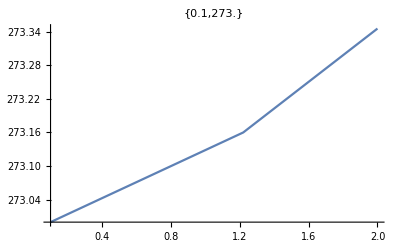

```mathematica
Quiet@Module[{pressure},pressure=P12;Plot[pressure[x],{x,0.1,2},PlotLabel->{0.1,pressure[0.1]}]]
```

```mathematica
P13=Quiet@Interpolation[{{0.1,273},{1.32,273.16},{22.35,278.16},{43.33,283.16},{64.27,288.16},{85.18,293.16},{106.07,298.16},{126.96,303.16},{147.84,308.16},{168.72,313.16},{189.6,318.16},{210.49,323.16},{231.39,328.16},{252.3,333.16},{273.21,338.16},{294.14,343.16},{315.09,348.16},{336.05,353.16},{357.03,358.16},{378.03,363.16},{399.06,368.16},{420.11,373.16},{441.19,378.16},{462.3,383.16},{483.44,388.16},{504.63,393.16},{525.85,398.16},{547.12,403.16},{568.44,408.16},{589.81,413.16},{611.24,418.16},{632.73,423.16},{654.29,428.16},{675.91,433.16},{697.62,438.16},{719.4,443.16},{741.28,448.16},{763.25,453.16},{785.32,458.16},{807.5,463.16},{814.6,464.75},{2786.5,464.75},{2796.1,468.16},{2809.7,473.16},{2822.8,478.16},{2835.7,483.16},{2848.3,488.16},{2860.7,493.16},{2872.9,498.16},{2884.9,503.16},{2896.8,508.16},{2908.6,513.16},{2920.2,518.16},{2931.8,523.16},{2943.2,528.16},{2954.6,533.16},{2965.9,538.16},{2977.2,543.16},{2988.4,548.16},{2999.5,553.16},{3010.6,558.16},{3021.7,563.16},{3032.7,568.16},{3043.7,573.16},{3054.6,578.16},{3065.5,583.16},{3076.4,588.16},{3087.3,593.16},{3098.1,598.16},{3109.,603.16},{3119.8,608.16},{3130.6,613.16},{3141.4,618.16},{3152.2,623.16},{3162.9,628.16},{3173.7,633.16},{3184.5,638.16},{3195.2,643.16},{3206.,648.16}},InterpolationOrder->1];
```

```mathematica
P14=Quiet@Interpolation[{{0.1,273},{1.42,273.16},{22.45,278.16},{43.43,283.16},{64.36,288.16},{85.27,293.16},{106.16,298.16},{127.05,303.16},{147.93,308.16},{168.81,313.16},{189.69,318.16},{210.58,323.16},{231.48,328.16},{252.38,333.16},{273.3,338.16},{294.23,343.16},{315.17,348.16},{336.13,353.16},{357.11,358.16},{378.11,363.16},{399.13,368.16},{420.18,373.16},{441.26,378.16},{462.37,383.16},{483.52,388.16},{504.7,393.16},{525.92,398.16},{547.19,403.16},{568.51,408.16},{589.88,413.16},{611.3,418.16},{632.79,423.16},{654.35,428.16},{675.97,433.16},{697.67,438.16},{719.46,443.16},{741.33,448.16},{763.3,453.16},{785.37,458.16},{807.54,463.16},{829.84,468.16},{829.97,468.19},{2788.8,468.19},{2803.,473.16},{2816.6,478.16},{2829.9,483.16},{2842.8,488.16},{2855.5,493.16},{2868.,498.16},{2880.2,503.16},{2892.4,508.16},{2904.3,513.16},{2916.2,518.16},{2927.9,523.16},{2939.5,528.16},{2951.,533.16},{2962.5,538.16},{2973.9,543.16},{2985.2,548.16},{2996.4,553.16},{3007.6,558.16},{3018.8,563.16},{3029.9,568.16},{3040.9,573.16},{3052.,578.16},{3063.,583.16},{3073.9,588.16},{3084.9,593.16},{3095.8,598.16},{3106.7,603.16},{3117.6,608.16},{3128.4,613.16},{3139.3,618.16},{3150.1,623.16},{3160.9,628.16},{3171.8,633.16},{3182.6,638.16},{3193.4,643.16},{3204.2,648.16}},InterpolationOrder->1];
```

```mathematica
P15=Quiet@Interpolation[{{0.1,273},{1.53,273.16},{22.55,278.16},{43.52,283.16},{64.46,288.16},{85.36,293.16},{106.26,298.16},{127.14,303.16},{148.02,308.16},{168.9,313.16},{189.78,318.16},{210.67,323.16},{231.56,328.16},{252.46,333.16},{273.38,338.16},{294.31,343.16},{315.25,348.16},{336.21,353.16},{357.19,358.16},{378.19,363.16},{399.21,368.16},{420.26,373.16},{441.34,378.16},{462.44,383.16},{483.59,388.16},{504.77,393.16},{525.99,398.16},{547.26,403.16},{568.57,408.16},{589.94,413.16},{611.37,418.16},{632.85,423.16},{654.41,428.16},{676.03,433.16},{697.73,438.16},{719.51,443.16},{741.38,448.16},{763.35,453.16},{785.41,458.16},{807.59,463.16},{829.88,468.16},{844.56,471.44},{2791.,471.44},{2796.,473.16},{2810.2,478.16},{2823.9,483.16},{2837.2,488.16},{2850.2,493.16},{2863.,498.16},{2875.5,503.16},{2887.8,508.16},{2900.,513.16},{2912.,518.16},{2923.9,523.16},{2935.7,528.16},{2947.4,533.16},{2959.,538.16},{2970.5,543.16},{2981.9,548.16},{2993.3,553.16},{3004.6,558.16},{3015.9,563.16},{3027.1,568.16},{3038.2,573.16},{3049.3,578.16},{3060.4,583.16},{3071.4,588.16},{3082.5,593.16},{3093.4,598.16},{3104.4,603.16},{3115.3,608.16},{3126.3,613.16},{3137.2,618.16},{3148.1,623.16},{3158.9,628.16},{3169.8,633.16},{3180.7,638.16},{3191.5,643.16},{3202.4,648.16}},InterpolationOrder->1];
```

```mathematica
P16=Quiet@Interpolation[{{0.1,273},{1.63,273.16},{22.650,278.16},{43.62,283.16},{64.55,288.16},{85.46,293.16},{106.35,298.16},{127.23,303.16},{148.11,308.16},{168.99,313.16},{189.87,318.16},{210.75,323.16},{231.65,328.16},{252.55,333.16},{273.46,338.16},{294.39,343.16},{315.33,348.16},{336.29,353.16},{357.27,358.16},{378.27,363.16},{399.29,368.16},{420.33,373.16},{441.41,378.16},{462.52,383.16},{483.66,388.16},{504.84,393.16},{526.06,398.16},{547.33,403.16},{568.64,408.16},{590.01,413.16},{611.43,418.16},{632.92,423.16},{654.47,428.16},{676.09,433.16},{697.79,438.16},{719.57,443.16},{741.44,448.16},{763.4,453.16},{785.46,458.16},{807.63,463.16},{829.92,468.16},{852.33,473.16},{858.46,474.52},{2792.8,474.52},{2803.6,478.16},{2817.8,483.16},{2831.5,488.16},{2844.8,493.16},{2857.8,498.16},{2870.6,503.16},{2883.2,508.16},{2895.6,513.16},{2907.8,518.16},{2919.9,523.16},{2931.9,528.16},{2943.7,533.16},{2955.5,538.16},{2967.1,543.16},{2978.7,548.16},{2990.1,553.16},{3001.6,558.16},{3012.9,563.16},{3024.2,568.16},{3035.5,573.16},{3046.7,578.16},{3057.8,583.16},{3068.9,588.16},{3080.,593.16},{3091.1,598.16},{3102.1,603.16},{3113.1,608.16},{3124.1,613.16},{3135.1,618.16},{3146.,623.16},{3156.9,628.16},{3167.9,633.16},{3178.8,638.16},{3189.7,643.16},{3200.5,648.16}},InterpolationOrder->1];
```

```mathematica
P17=Quiet@Interpolation[{{0.1,273},{1.73,273.16},{22.75,278.16},{43.72,283.16},{64.65,288.16},{85.55,293.16},{106.44,298.16},{127.32,303.16},{148.20,308.16},{169.07,313.16},{189.95,318.16},{210.84,323.16},{231.73,328.16},{252.63,333.16},{273.55,338.16},{294.47,343.16},{315.41,348.16},{336.37,353.16},{357.35,358.16},{378.34,363.16},{399.36,368.16},{420.41,373.16},{441.48,378.16},{462.59,383.16},{483.73,388.16},{504.91,393.16},{526.13,398.16},{547.39,403.16},{568.71,408.16},{590.07,413.16},{611.49,418.16},{632.98,423.16},{654.53,428.16},{676.15,433.16},{697.84,438.16},{719.62,443.16},{741.49,448.16},{763.45,453.16},{785.51,458.16},{807.68,463.16},{829.96,468.16},{852.37,473.16},{871.74,477.46},{2794.5,477.46},{2796.6,478.16},{2811.4,483.16},{2825.5,488.16},{2839.3,493.16},{2852.6,498.16},{2865.7,503.16},{2878.5,508.16},{2891.1,513.16},{2903.6,518.16},{2915.9,523.16},{2928.,528.16},{2940.,533.16},{2951.9,538.16},{2963.7,543.16},{2975.3,548.16},{2987.,553.16},{2998.5,558.16},{3009.9,563.16},{3021.3,568.16},{3032.7,573.16},{3044.,578.16},{3055.2,583.16},{3066.4,588.16},{3077.6,593.16},{3088.7,598.16},{3099.8,603.16},{3110.9,608.16},{3121.9,613.16},{3132.9,618.16},{3143.9,623.16},{3154.9,628.16},{3165.9,633.16},{3176.8,638.16},{3187.8,643.16},{3198.7,648.16}},InterpolationOrder->1];
```

```mathematica
P18=Quiet@Interpolation[{{0.1,273},{1.83,273.16},{22.85,278.16},{43.82,283.16},{64.74,288.16},{85.65,293.16},{106.53,298.16},{127.41,303.16},{148.29,308.16},{169.16,313.16},{190.04,318.16},{210.92,323.16},{231.82,328.16},{252.72,333.16},{273.63,338.16},{294.55,343.16},{315.49,348.16},{336.45,353.16},{357.42,358.16},{378.42,363.16},{399.44,368.16},{420.48,373.16},{441.56,378.16},{462.66,383.16},{483.8,388.16},{504.98,393.16},{526.2,398.16},{547.46,403.16},{568.77,408.16},{590.14,413.16},{611.56,418.16},{633.04,423.16},{654.59,428.16},{676.21,433.16},{697.9,438.16},{719.68,443.16},{741.54,448.16},{763.5,453.16},{785.56,458.16},{807.73,463.16},{830.01,468.16},{852.41,473.16},{874.96,478.16},{884.47,480.26},{2795.9,480.26},{2804.7,483.16},{2819.4,488.16},{2833.6,493.16},{2847.3,498.16},{2860.6,503.16},{2873.7,508.16},{2886.6,513.16},{2899.2,518.16},{2911.7,523.16},{2924.,528.16},{2936.2,533.16},{2948.2,538.16},{2960.2,543.16},{2972.,548.16},{2983.7,553.16},{2995.4,558.16},{3006.9,563.16},{3018.4,568.16},{3029.9,573.16},{3041.3,578.16},{3052.6,583.16},{3063.9,588.16},{3075.1,593.16},{3086.3,598.16},{3097.5,603.16},{3108.6,608.16},{3119.7,613.16},{3130.8,618.16},{3141.9,623.16},{3152.9,628.16},{3163.9,633.16},{3174.9,638.16},{3185.9,643.16},{3196.9,648.16}},InterpolationOrder->1];
```

```mathematica
P19=Quiet@Interpolation[{{0.1,273},{1.93,273.16},{22.95,278.16},{43.91,283.16},{64.84,288.16},{85.74,293.16},{106.63,298.16},{127.5,303.16},{148.38,308.16},{169.25,313.16},{190.13,318.16},{211.01,323.16},{231.9,328.16},{252.8,333.16},{273.71,338.16},{294.64,343.16},{315.57,348.16},{336.53,353.16},{357.5,358.16},{378.5,363.16},{399.52,368.16},{420.56,373.16},{441.63,378.16},{462.74,383.16},{483.87,388.16},{505.05,393.16},{526.27,398.16},{547.53,403.16},{568.84,408.16},{590.2,413.16},{611.62,418.16},{633.1,423.16},{654.65,428.16},{676.27,433.16},{697.96,438.16},{719.73,443.16},{741.59,448.16},{763.55,453.16},{785.61,458.16},{807.77,463.16},{830.05,468.16},{852.46,473.16},{874.99,478.16},{896.71,482.95},{2797.2,482.95},{2797.8,483.16},{2813.1,488.16},{2827.7,493.16},{2841.8,498.16},{2855.5,503.16},{2868.9,508.16},{2882.,513.16},{2894.8,518.16},{2907.5,523.16},{2920.,528.16},{2932.4,533.16},{2944.6,538.16},{2956.6,543.16},{2968.6,548.16},{2980.5,553.16},{2992.2,558.16},{3003.9,563.16},{3015.5,568.16},{3027.1,573.16},{3038.5,578.16},{3049.9,583.16},{3061.3,588.16},{3072.6,593.16},{3083.9,598.16},{3095.1,603.16},{3106.3,608.16},{3117.5,613.16},{3128.7,618.16},{3139.8,623.16},{3150.9,628.16},{3161.9,633.16},{3173.,638.16},{3184.,643.16},{3195.1,648.16}},InterpolationOrder->1];
```

```mathematica
P20=Quiet@Interpolation[{{0.1,273},{2.0300,273.16},{23.05,278.16},{44.01,283.16},{64.94,288.16},{85.83,293.16},{106.72,298.16},{127.59,303.16},{148.47,308.16},{169.34,313.16},{190.22,318.16},{211.1,323.16},{231.99,328.16},{252.88,333.16},{273.79,338.16},{294.72,343.16},{315.65,348.16},{336.61,353.16},{357.58,358.16},{378.58,363.16},{399.59,368.16},{420.64,373.16},{441.71,378.16},{462.81,383.16},{483.95,388.16},{505.12,393.16},{526.34,398.16},{547.6,403.16},{568.91,408.16},{590.27,413.16},{611.69,418.16},{633.16,423.16},{654.71,428.16},{676.32,433.16},{698.01,438.16},{719.79,443.16},{741.65,448.16},{763.6,453.16},{785.65,458.16},{807.82,463.16},{830.09,468.16},{852.5,473.16},{875.03,478.16},{897.71,483.16},{908.5,485.53},{2798.3,485.53},{2806.6,488.16},{2821.7,493.16},{2836.2,498.16},{2850.2,503.16},{2863.9,508.16},{2877.3,513.16},{2890.4,518.16},{2903.3,523.16},{2916.,528.16},{2928.5,533.16},{2940.9,538.16},{2953.1,543.16},{2965.2,548.16},{2977.2,553.16},{2989.1,558.16},{3000.9,563.16},{3012.6,568.16},{3024.2,573.16},{3035.8,578.16},{3047.3,583.16},{3058.7,588.16},{3070.1,593.16},{3081.5,598.16},{3092.8,603.16},{3104.1,608.16},{3115.3,613.16},{3126.5,618.16},{3137.7,623.16},{3148.8,628.16},{3160.,633.16},{3171.1,638.16},{3182.1,643.16},{3193.2,648.16}},InterpolationOrder->1];
```

```mathematica
vspring[r_,y1_,y2_]:=Module[{n,h,yvalues,xvalues},
n=150;h=(y2-y1)/n;
yvalues=Table[k,{k,y1,y2,h}];
xvalues=Table[r*Sin[m*π/2],{m,0,n}];
Line[Transpose@{xvalues,yvalues}]
];
```





```mathematica
Manipulate[
Module[{P1,H,HL,HV,quality,y,x,pressure,T2,step,spring,bars},
P1=20;H=H1T[T1+273];HL=HLP[P2];HV=HVP[P2];

quality=(H-HL)/(HV-HL);
y=If[quality<0,0,quality];x=1-y;

(*pressure=Switch[P2,0.1,P01,0.2,P02,0.3,P03,0.4,P04,0.5,P05,0.6,P06,0.7,P07,0.8,P08,0.9,P09,1.0,P10,1.1,P11,1.2,P12,1.3,P13,1.4,P14,1.5,P15,1.6,P16,1.7,P17,1.8,P18,1.90,P19,2.0,P20][H];*)
(*pressure=Switch[P2,0.1,P01[H],0.2,P02[H],0.3,P03[H],0.4,P04[H],0.5,P05[H],0.6,P06[H],0.7,P07[H],0.8,P08[H],0.9,P09[H],1.0,P10[H],1.1,P11[H],1.2,P12[H],1.3,P13[H],1.4,P14[H],1.5,P15[H],1.6,P16[H],1.7,P17[H],1.8,P18[H],1.90,P19[H],2.0,P20[H]];*)
(*pressure=Which[P2==0.1,P01,P2==0.2,P02,P2==0.3,P03,P2=0.4,P04,P2=0.5,P05,P2=0.6,P06,P2==0.7,P07,P2==0.8,P08,P2==0.9,P09,P2==1,P10,P2==1.1,P11,P2==1.2,P12,P2==1.3,P13,P2==1.4,P14,P2==1.5,P15,P2==1.6,P16,P2==1.7,P17,P2==1.8,P18,P2==1.9,P19,P2==2,P20][H];*)
pressure=Which[P2==0.1,P01[H],P2==0.2,P02[H],P2==0.3,P03[H],P2==0.4,P04[H],P2==0.5,P05[H],P2==0.6,P06[H],P2==0.7,P07[H],P2==0.8,P08[H],P2==0.9,P09[H],P2==1,P10[H],P2==1.1,P11[H],P2==1.2,P12[H],P2==1.3,P13[H],P2==1.4,P14[H],P2==1.5,P15[H],P2==1.6,P16[H],P2==1.7,P17[H],P2==1.8,P18[H],P2==1.9,P19[H],P2==2,P20[H]];
T2=If[y==0,pressure,TP[P2]]-273;

step=Rescale[P2,{0.1,9}];

spring=Graphics[{Thick,Darker[Gray,0.5],vspring[0.12,0,1.75]}];

bars=BarChart[{x,y},ChartStyle->{RGBColor[0.35,0.6,1],Green},PlotRange->{{0.5,2.5},{0,1}},
Frame->{{True,None},{True,None}},LabelStyle->{17,Black},ChartLabels->Placed[{"liquid",If[y>0.08,"vapor",""]},Center],ImageSize->{210,210},AspectRatio->Full];

Graphics[{
{RGBColor[1,0.95,0.47],FilledCurve[{Line[{{-1,0},{3,0},{3,1.5},{5,1.5},{5,0},{9,0},{9,-3},{-1,-3}}]}]},
Inset[spring,{4,1.05+step*2.25}],
{Thick,EdgeForm@Black,FaceForm@Lighter[Gray,0.5],Polygon[{{3.5,-0.75+step*2.25},{4.5,-0.75+step*2.25},{4.25,-1.5+step*2.25},{3.75,-1.5+step*2.25}}]},
{EdgeForm@Black,Gray,FilledCurve[{Line[{{-1,0},{3,0},{3,1.5},{5,1.5},{5,0},{9,0},{9,-0.5},{4.5,-0.5},{4.5,1},{3.5,1},{3.5,-1.5},{3.6,-1.5},{3.6,-1.6},{3,-1.6},{3,-0.5},{-1,-0.5},{-1,0}}]}],
FilledCurve[{Line[{{-1,-3},{4.5,-3},{4.5,-1.6},{4.4,-1.6},{4.4,-1.5},{5,-1.5},{5,-3},{9,-3},{9,-3.5},{-1,-3.5},{-1,-3}}]}]},
{Darker[Gray,0.5],Thickness@0.022,Line[{{4,3.14+step*2.25},{4.,3.1+step*2.25}}]},
{Thick,EdgeForm@Black,FaceForm@Lighter[Gray,0.5],Polygon[{{2.75,2.85+step*2.25},{5.25,2.85+step*2.25},{5,3.1+step*2.25},{3,3.1+step*2.25}}]},
Inset[bars,{7.2,1.8}],
(**)
Text[Style["fraction of liquid and vapor exiting",17],{7,3.85}],
Text[Style[Column[{
Row@{Subsuperscript[Style["P",Italic],#1,""]," = ",#2," MPa"},
Row@{Subsuperscript[Style["T",Italic],#1,""]," = ",NumberForm[#3,{3,0}]," °C"},
Spacer@15,#4},Center],22],{#5,-1.85}]&@@@{{1,P1,T1,"liquid water",1},{2,P2,T2,If[y==0,"liquid water","vapor/liquid mixture"],7}}
},PlotRange->{{-1,9.1},{-3.5,4}},ImageSize->{600,430},AspectRatio->Full,PlotLabel->{H,P15[H]}]
],
Grid[{{
Control[{{T1,227,"inlet temperature (°C)"},100,312,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{P2,0.5,"outlet pressure (MPa)"},0.1,2,0.1,Appearance->"Labeled",ImageSize->Small}]
}}],
SaveDefinitions->True]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX